# Numerical Methods - Problem Set 7

## Problem 4

## a)

```mathematica
f[x_] = x + x^3
```

x+x^3

```mathematica
Integrate[f[x],{x,0,1}]
```

3/4

```mathematica
a =  0
b = 1
n = 5 (*number of points, not intervals*)
h = (b - a)/(n-1)
```

0

1

5

1/4

```mathematica
xVals = Table[a + i * h, {i,0,n-1}]
fVals = Table[f[a + i * h], {i, 0, n-1}]
```

{0,1/4,1/2,3/4,1}

{0,17/64,5/8,75/64,2}

```mathematica
N[fVals]
```

{0.,0.265625,0.625,1.17188,2.}

## b)

```mathematica
(* Given values *)
L = 2;
w1 = 3;
w2 = 4.5
```

4.5

```mathematica
(* Defining the wave equation, the derived probability, and the fourth derivative of the probability with respect to x for error caluclation *)
Psi[x_,t_]= 1/Sqrt[L] (Sin[(Pi x)/L] Exp[-ⅈ w1 t] + Sin[(2 Pi x)/L] Exp[- ⅈ w2 t]);
Prob[x_,t_]= Simplify[ComplexExpand[(Abs[Psi[x,t]])^2]];
dProb[x_,t_]=Derivative[4,0][Prob][x,t];
```

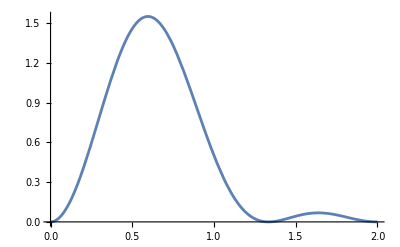

```mathematica
Plot[Prob[x,0],{x,0,L}]
```

```mathematica
Integrate[Prob[x,0],{x,(3 L)/4, L}]
```

0.0203698

```mathematica
(* Defining the bounds of integration and the step size *)
a =  (3 L)/4;
b = L;
h[num_] := (b - a)/(num-1)
```

```mathematica
(* Calculating the value of the probability at different x and writing it to a list *)
fVals[num_,t_] := Table[Prob[a + i * h[num],t], {i, 0, num-1}]
(* Numerically calculating the integral using num_ points at a time t_ *)
intProb[num_,t_] := h[num]/3(fVals[num,t][[1]] 
+ fVals[num,t][[num]] 
+ 4 Sum[Prob[a + (2 i - 1) h[num], t],{i,1,(num-1)/2}]
+ 2 Sum[Prob[a + (2i) h[num], t],{i, 1, (num-1)/2 - 1}])
(* Calculating the error using the given formula *)
error[num_,t_]:=Re[1/90 h[num]^4 dProb[a,t]]
```

```mathematica
(* Creating tables for the integral values, ln(E), and ln(h) for plotting *)
intVals = Table[intProb[2i + 1, 0],{i,5, (101 - 1)/2}];
errVals = Table[Log[error[i, 0]],{i, 5, 501}];
errVals2 = Table[Log[error[i, Pi/(w2 - w1)]],{i, 5, 501}];
hVals = Table[N[Log[h[i]]],{i, 5, 501}];
```

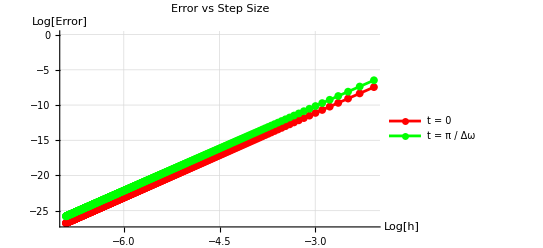

```mathematica
(* Place hvals and errVals into pairs *)data=Transpose[{hVals,errVals}];
data2=Transpose[{hVals,errVals2}];

(* Create the plots *)
ListPlot[
{data, data2},
PlotStyle->{Red, Green},
PlotMarkers->{"●",8},
AxesLabel->{"Log[h]","Log[Error]"},
PlotLabel->"Error vs Step Size",
GridLines->Automatic,
Joined->True,
PlotLegends->{"t = 0","t = π / Δω"}
]
```

## Problem 5

```mathematica
func1[x_]:=Exp[x] Cos[x]
func2[x_] := Exp[x]
func3[x_] := Piecewise[{{Exp[2 x], x < 0}, {x - 2 Cos[x] + 4, x >= 0}}]
```

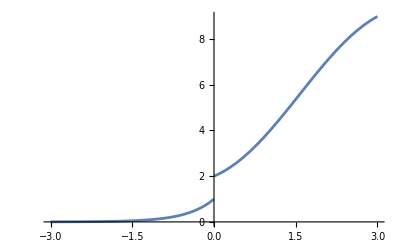

```mathematica
Plot[func3[x],{x,-3,3}]
```

```mathematica
I1[x_]:= Integrate[func1[x],x]
```

```mathematica
Integrate[func1[x],{x,0,Pi/2}]
```

1/2 (-1+ⅇ^(π/2))

```mathematica
N[1/2 (-1+ⅇ^(π/2))]
```

1.90524

```mathematica
NumberForm[1.9052386904826757,16]
```

1.905238690482676

```mathematica
Integrate[func2[x],{x,-1,3}]
```

(-1+ⅇ^4)/ⅇ

```mathematica
N[(-1+ⅇ^4)/ⅇ]
```

19.7177

```mathematica
NumberForm[19.717657482016225,16]
```

19.71765748201623

```mathematica
Integrate[func3[x],{x,-1,1}]
```

(-1+10 ⅇ^2-4 ⅇ^2 Sin[1])/(2 ⅇ^2)

```mathematica
N[(-1+10 ⅇ^2-4 ⅇ^2 Sin[1])/(2 ⅇ^2)]
```

3.24939

```mathematica
NumberForm[3.2493903887659017,16]
```

3.249390388765902